# Plots zu höheren Dimensionen

Aufbauend auf den “remant-plot.nb” fuer die Masterthesis hier Plots, die verschiedene Wahlen von n (Anzahl Extradimensionen) abdecken.

## Schwarzschild-Tangherlini

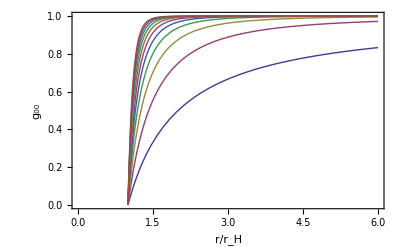

```mathematica
(* Ordinary Schwarzschild in higher Dimensions *)
Plot[
Evaluate@With[{
rH=((n+2)/2)^(1/(1+n))},
Table[1- 2/(n+2)(rH/r)^(1+n),{n,0,10}]],
{r,0,6},
PlotRange-> {0,1},
FrameLabel-> {"r/r_H", "g_00"},
Frame->True
]
```

## Neu: Holo-Plot für höhere Dimensionen

```mathematica
holoN[z_,n_]:=z^(2+n)/(z^(2+n) +1)
g00N[z_, n_, M_, func_] := 1 - 2/(n+2) M func[z,n]/z^(1+n)
STM[z_,n_] = 1; (* STM: Schwarzschild Tangherlini Metrik *)
```

### Dimensionen variabel

```mathematica
Plot[{
g00N[z,n,(n+2)/2,holoN],
g00N[z,n,(n+2)/2,STM]
},
{z,0,5},
PlotRange-> {-0.5,1},
FrameLabel->{"r/L", "g_00"},
PlotRangePadding-> None,
Frame-> True,
AspectRatio-> 0.5,
ImageSize-> Full
]~Manipulate~{n,0,7}
```

```mathematica
nchoices = Range[0,7];
holoNGraphs[z_] = g00N[z,#,1, holoN] &/@ nchoices (* must be function for EpiLabels *)
STMGraphs = g00N[z,#,1,STM] & /@nchoices
holoNCompareFuncs= Join[holoNGraphs[z],STMGraphs];
```

{1-z/(1+z^2),1-(2 z)/(3 (1+z^3)),1-z/(2 (1+z^4)),1-(2 z)/(5 (1+z^5)),1-z/(3 (1+z^6)),1-(2 z)/(7 (1+z^7)),1-z/(4 (1+z^8)),1-(2 z)/(9 (1+z^9))}

{1-1/z,1-2/(3 z^2),1-1/(2 z^3),1-2/(5 z^4),1-1/(3 z^5),1-2/(7 z^6),1-1/(4 z^7),1-2/(9 z^8)}

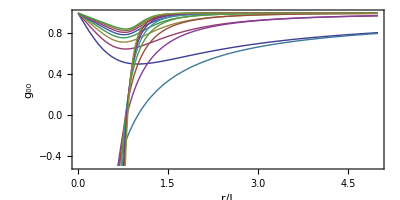

```mathematica
Plot[Evaluate@holoNCompareFuncs,
{z,0,5},
PlotRange-> {-0.5,1},
FrameLabel->{"r/L", "g_00"},
PlotRangePadding-> None,
Frame-> True,
AspectRatio-> 0.5,
ImageSize-> Full
]
```